# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

Narišite graf funkcije y=a sin (k x+n) tako, da boste lahko vrednosti parametrov a, k in n spreminjali v obsegu od -3 do 3. Območje risanja omejite na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
(* V funkciji Plot uporabite nastavitvi Range->{-5,5} in AspectRatio->Automatic *)
Manipulate[
Plot[a Sin[k x+n],{x,-5,5},AspectRatio->Automatic],
{{a,1},-3,3},{{k,1},-3,3},{{n,1},-3,3}]
```

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
Manipulate[
Plot[{k x+n,-k x+k Subscript[x, 0]+Subscript[y, 0]},{x,-5,5},AspectRatio->Automatic,
Epilog->{PointSize[Large],Point[{{Subscript[x, 0],Subscript[y, 0]}}]}],
{{k,1},-5,5},{{n,1},-5,5},{{Subscript[x, 0],1},-5,5},{{Subscript[y, 0],1},-5,5}]
```

### Subsection. naloga:

Definirajte funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter narišite njen graf skupaj s tangento v točki x_0, tako da boste lahko spreminjali vrednosti parametra x_0. Na sliki označite z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
f[x_]:=(x(x-2)^2)/(x^2+1);
Manipulate[
Plot[{f[x],f'[Subscript[x, 0]] (x-Subscript[x, 0])+f[Subscript[x, 0]]},{x,-15,15},AspectRatio->Automatic,
Epilog->{PointSize[Large],Point[{{Subscript[x, 0],f[Subscript[x, 0]]}}]}],
{{Subscript[x, 0],1},-5,5}]
```

Set::write: Tag Plus in 1+Abs[5. k+n]^(2/3) is Protected.

Set::write: Tag Plus in 6.08204+Abs[5. k+n]^(2/3) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Plus in 1+Abs[5. k+n]^(2/3) is Protected.

Set::write: Tag Plus in 6.08204+Abs[5. k+n]^(2/3) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Plus in 1+Abs[5. k+n]^(2/3) is Protected.

Set::write: Tag Plus in 6.08204+Abs[5. k+n]^(2/3) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Plus in 1+Abs[5. k+n]^(2/3) is Protected.

Set::write: Tag Plus in 6.08204+Abs[5. k+n]^(2/3) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Plus in 1+Abs[5. k+n]^(2/3) is Protected.

Set::write: Tag Plus in 6.08204+Abs[5. k+n]^(2/3) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Plus in 1+Abs[5. k+n]^(2/3) is Protected.

Set::write: Tag Plus in 6.08204+Abs[5. k+n]^(2/3) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

### Subsection. naloga:

1. Narišite graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]
2. Prikažite, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.
3. Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

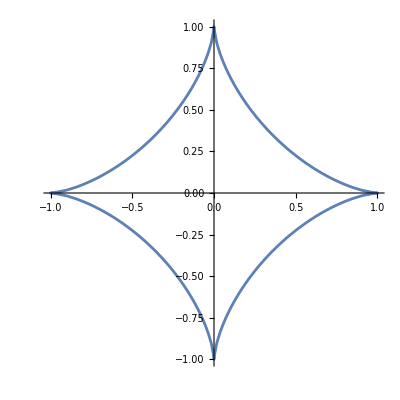

```mathematica
ClearAll;
graf1=ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1,
{x,-1,1},{y,-1,1},
Axes->True ,Frame->False]
graf2=Manipulate[ContourPlot[Abs[x]^p+Abs[y]^p==1,
{x,-1,1},{y,-1,1},
Axes->True ,Frame->False],
{{p,2},0,4}]
```

## Vektorji in matrike

### Subsection. naloga:

1. Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.
2. Izračunaj njun skalarni produkt.
3. Izračunaj njun vektorski produkt.
4. Kateri od vektorjev je daljši?
5. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
Subscript[v, 1]={1,2,3}
Subscript[v, 2]={-3,-2,5}
Subscript[v, 1].Subscript[v, 2]
Cross[Subscript[v, 1],Subscript[v, 2]]
Norm[Subscript[v, 1]]
Norm[Subscript[v, 2]]
r={a,b,c};
Subscript[r, 0]={1,1,1};
Ravnina=(r-Subscript[r, 0])Cross[Subscript[v, 1],Subscript[v, 2]]==0
```

{1,2,3}

{-3,-2,5}

8

{16,-14,4}

√14

√38

{{16 (-1+a1),16 (-1+a2),16 (-1+a3)},{-14 (-1+b1),-14 (-1+b2),-14 (-1+b3)},{4 (-1+c1),4 (-1+c2),4 (-1+c3)}}==0

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
a={a1,a2,a3};
b={b1,b2,b3};
c= {c1,c2,c3};
Reduce[Cross[a,Cross[b,c]]==(a.c)b-(a.b)c]
```

True

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

```mathematica
A={{a1,c1},{b1,d1}};
B={{a2,c2},{b2,d2}};
Reduce[(A B)^-1==B^-1 A^-1]
```

True

### Subsection. naloga:

1. Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.
2. Izračunaj njeno determinanto.
3. Izračunaj njene lastne vrednosti.
4. Izračunaj njene lastne vektorje.
5. Ali je matrika diagonalizabilna?
6. Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.
7. Preveri, ali velja pogoj za diagonalizability.

```mathematica
ClearAll;
M={{9,3,6},{2,2,4},{-3,1,-1}}
Det[M]
lv=Eigenvalues[M]
Diag=DiagonalMatrix[lv]
Prehodna=Transpose[Diag]
IPrehodna=Inverse[Prehodna]
Reduce[M==Prehodna.Diag.IPrehodna]
```

{{9,3,6},{2,2,4},{-3,1,-1}}

-36

{3 (1+√2),4,3 (1-√2)}

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

{{1/36 (-12+12 √2),0,0},{0,1/4,0},{0,0,1/36 (-12-12 √2)}}

False